```mathematica
0.099*0.8
```

0.0792

```mathematica
Table[0,{i,2}]
```

{0,0}

```mathematica
{0.7,0.2,0.1}.markovChainMatrix
```

{0.66,0.24,0.1}

```mathematica
%.markovChainMatrix
```

{0.655556,0.244444,0.1}

```mathematica
markovChainMatrix[[1]]
```

{0.7,0.2,0.1}

```mathematica
markovChainMatrix[[3]].MatrixPower[markovChainMatrix,10]
```

{0.655556,0.244444,0.1}

```mathematica
%.markovChainMatrix
```

{0.655556,0.244444,0.1}

```mathematica
MatrixPower[markovChainMatrix,10]
```

{{0.655556,0.244444,0.1},{0.655556,0.244444,0.1},{0.655556,0.244444,0.1}}

```mathematica
markovChainMatrix[[1]].%
```

{0.655556,0.244444,0.1}

```mathematica
stateProb
```

{0.655556,0.244444,0.1}

```mathematica
Dimensions[wData]
```

{8759,27}

```mathematica
%[[1]]
```

8759

```mathematica
If[randomStateSequence[[1]]=="M", Print["yes"],Print["No"]]
```

yes

```mathematica
Length[availableResources]
```

2

```mathematica
For[i=1,i≤Length[availableResources],i++,
{availableResources[[i]] =  0.5*0.5*1.27*Pi*windSpeed[[10+i-1]]^3+1.2*100*solarRadi[[Mod[10+i-1,24]+1,month]]}
]
```

```mathematica
availableResources
```

{0,0}

```mathematica
availableResources
```

{2364.14,2295.29}

```mathematica
AvailableResource[100]
```

```mathematica
demand
```

{0,0}

```mathematica
Demand[100]
```

```mathematica
demand
```

{1042.13,1524.78}

```mathematica
x=3;
```

```mathematica
Minimize[2 x^2-3 x+5,x]
```

{31/8,{x→3/4}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
Symbol x
```

Symbol x

```mathematica
?Symbol
```

Symbol[name] refers to a symbol with the specified name.

```mathematica
Symbol["x"]
```

3

```mathematica
x
```

3

```mathematica
markovChainMatrix//Grid
```

0.7 | 0.2 | 0.1
0.6 | 0.3 | 0.1
0.5 | 0.4 | 0.1

```mathematica
markovChainMatrix[[2,1]]
```

0.6

```mathematica
Demand[t]
```

```mathematica
demand
```

```mathematica
{227.92606784937996,2621.6552462433383}
```

{227.926,2621.66}

```mathematica
AvailableResource[3]
```

2227.78

```mathematica
Demand[10]
```

3244.87

```mathematica
randomStateSequence[[t]]=="N"
```

True

```mathematica
Minimize[{0.051 (xGB+xGC)+0.002 (-xBC-xBG+xGB+xRB)+0.001 (xBC+xBG+xGB+xRB)-0.0408 (xBG+xRG)+0.7 (0.051 (yGB1+yGC1)+0.002 (-xBC-xBG+xGB+xRB-yBC1-yBG1+yGB1+yRB1)+0.001 (-xBC-xBG+xGB+xRB+yBC1+yBG1+yGB1+yRB1)-0.0408 (yBG1+yRG1))+0.6 (0.051 (yGB2+yGC2)+0.002 (-xBC-xBG+xGB+xRB-yBC2-yBG2+yGB2+yRB2)+0.001 (-xBC-xBG+xGB+xRB+yBC2+yBG2+yGB2+yRB2)-0.0408 (yBG2+yRG2))+0.5 (0.051 (yGB3+yGC3)+0.002 (-xBC-xBG+xGB+xRB-yBC3-yBG3+yGB3+yRB3)+0.001 (-xBC-xBG+xGB+xRB+yBC3+yBG3+yGB3+yRB3)-0.0408 (yBG3+yRG3)),xBC+xGC+xRC==265.5451903286421&&0≤-xBC-xBG+xGB+xRB≤capBat&&xRB+xRC+xRG==2364.1404817351918&&xGB≥0&&xGC≥0&&xRB≥0&&xRC≥0&&xRG≥0&&xBC≥0&&xBG≥0&&yGB1≥0&&yGC1≥0&&yRB1≥0&&yRC1≥0&&yRG1≥0&&yBC1≥0&&yBG1≥0&&yBC1+yGC1+yRC1==9291.418969944281&&xBC+xBG-xGB-xRB≤-yBC1-yBG1+yGB1+yRB1≤capBat+xBC+xBG-xGB-xRB&&yRB1+yRC1+yRG1==2295.2864117800195&&yGB2≥0&&yGC2≥0&&yRB2≥0&&yRC2≥0&&yRG2≥0&&yBC2≥0&&yBG2≥0&&yBC2+yGC2+yRC2==7400.271050457528&&xBC+xBG-xGB-xRB≤-yBC2-yBG2+yGB2+yRB2≤capBat+xBC+xBG-xGB-xRB&&yRB2+yRC2+yRG2==2295.2864117800195&&yGB3≥0&&yGC3≥0&&yRB3≥0&&yRC3≥0&&yRG3≥0&&yBC3≥0&&yBG3≥0&&yBC3+yGC3+yRC3==7008.120652501304&&xBC+xBG-xGB-xRB≤-yBC3-yBG3+yGB3+yRB3≤capBat+xBC+xBG-xGB-xRB&&yRB3+yRC3+yRG3==2295.2864117800195},{xGB,xGC,xRB,xRC,xRG,xBC,xBG,yGB1,yGC1,yRB1,yRC1,yRG1,yBC1,yBG1,yGB2,yGC2,yRB2,yRC2,yRG2,yBC2,yBG2,yGB3,yGC3,yRB3,yRC3,yRG3,yBC3,yBG3}]
```

Minimize[{0.051 (xGB+xGC)+0.002 (-xBC-xBG+xGB+xRB)+0.001 (xBC+xBG+xGB+xRB)-0.0408 (xBG+xRG)+0.7 (0.051 (yGB1+yGC1)+0.002 (-xBC-xBG+xGB+xRB-yBC1-yBG1+yGB1+yRB1)+0.001 (-xBC-xBG+xGB+xRB+yBC1+yBG1+yGB1+yRB1)-0.0408 (yBG1+yRG1))+0.6 (0.051 (yGB2+yGC2)+0.002 (-xBC-xBG+xGB+xRB-yBC2-yBG2+yGB2+yRB2)+0.001 (-xBC-xBG+xGB+xRB+yBC2+yBG2+yGB2+yRB2)-0.0408 (yBG2+yRG2))+0.5 (0.051 (yGB3+yGC3)+0.002 (-xBC-xBG+xGB+xRB-yBC3-yBG3+yGB3+yRB3)+0.001 (-xBC-xBG+xGB+xRB+yBC3+yBG3+yGB3+yRB3)-0.0408 (yBG3+yRG3)),xBC+xGC+xRC==265.545&&0≤-xBC-xBG+xGB+xRB≤capBat&&xRB+xRC+xRG==2364.14&&xGB≥0&&xGC≥0&&xRB≥0&&xRC≥0&&xRG≥0&&xBC≥0&&xBG≥0&&yGB1≥0&&yGC1≥0&&yRB1≥0&&yRC1≥0&&yRG1≥0&&yBC1≥0&&yBG1≥0&&yBC1+yGC1+yRC1==9291.42&&xBC+xBG-xGB-xRB≤-yBC1-yBG1+yGB1+yRB1≤capBat+xBC+xBG-xGB-xRB&&yRB1+yRC1+yRG1==2295.29&&yGB2≥0&&yGC2≥0&&yRB2≥0&&yRC2≥0&&yRG2≥0&&yBC2≥0&&yBG2≥0&&yBC2+yGC2+yRC2==7400.27&&xBC+xBG-xGB-xRB≤-yBC2-yBG2+yGB2+yRB2≤capBat+xBC+xBG-xGB-xRB&&yRB2+yRC2+yRG2==2295.29&&yGB3≥0&&yGC3≥0&&yRB3≥0&&yRC3≥0&&yRG3≥0&&yBC3≥0&&yBG3≥0&&yBC3+yGC3+yRC3==7008.12&&xBC+xBG-xGB-xRB≤-yBC3-yBG3+yGB3+yRB3≤capBat+xBC+xBG-xGB-xRB&&yRB3+yRC3+yRG3==2295.29},{xGB,xGC,xRB,xRC,xRG,xBC,xBG,yGB1,yGC1,yRB1,yRC1,yRG1,yBC1,yBG1,yGB2,yGC2,yRB2,yRC2,yRG2,yBC2,yBG2,yGB3,yGC3,yRB3,yRC3,yRG3,yBC3,yBG3}]

```mathematica
Minimize[{0.051 (xGB+xGC)+0.002 (-xBC-xBG+xGB+xRB)+0.001 (xBC+xBG+xGB+xRB)-0.0408 (xBG+xRG)+0.7 (0.051 (yGB1+yGC1)+0.002 (-xBC-xBG+xGB+xRB-yBC1-yBG1+yGB1+yRB1)+0.001 (-xBC-xBG+xGB+xRB+yBC1+yBG1+yGB1+yRB1)-0.0408 (yBG1+yRG1))+0.6 (0.051 (yGB2+yGC2)+0.002 (-xBC-xBG+xGB+xRB-yBC2-yBG2+yGB2+yRB2)+0.001 (-xBC-xBG+xGB+xRB+yBC2+yBG2+yGB2+yRB2)-0.0408 (yBG2+yRG2))+0.5 (0.051 (yGB3+yGC3)+0.002 (-xBC-xBG+xGB+xRB-yBC3-yBG3+yGB3+yRB3)+0.001 (-xBC-xBG+xGB+xRB+yBC3+yBG3+yGB3+yRB3)-0.0408 (yBG3+yRG3)),xBC+xGC+xRC==265.545&&0≤-xBC-xBG+xGB+xRB≤capBat&&xRB+xRC+xRG==2364.14&&xGB≥0&&xGC≥0&&xRB≥0&&xRC≥0&&xRG≥0&&xBC≥0&&xBG≥0&&yGB1≥0&&yGC1≥0&&yRB1≥0&&yRC1≥0&&yRG1≥0&&yBC1≥0&&yBG1≥0&&yBC1+yGC1+yRC1==9291.42&&xBC+xBG-xGB-xRB≤-yBC1-yBG1+yGB1+yRB1≤capBat+xBC+xBG-xGB-xRB&&yRB1+yRC1+yRG1==2295.29&&yGB2≥0&&yGC2≥0&&yRB2≥0&&yRC2≥0&&yRG2≥0&&yBC2≥0&&yBG2≥0&&yBC2+yGC2+yRC2==7400.27&&xBC+xBG-xGB-xRB≤-yBC2-yBG2+yGB2+yRB2≤capBat+xBC+xBG-xGB-xRB&&yRB2+yRC2+yRG2==2295.29&&yGB3≥0&&yGC3≥0&&yRB3≥0&&yRC3≥0&&yRG3≥0&&yBC3≥0&&yBG3≥0&&yBC3+yGC3+yRC3==7008.12&&xBC+xBG-xGB-xRB≤-yBC3-yBG3+yGB3+yRB3≤capBat+xBC+xBG-xGB-xRB&&yRB3+yRC3+yRG3==2295.29},{xGB,xGC,xRB,xRC,xRG,xBC,xBG,yGB1,yGC1,yRB1,yRC1,yRG1,yBC1,yBG1,yGB2,yGC2,yRB2,yRC2,yRG2,yBC2,yBG2,yGB3,yGC3,yRB3,yRC3,yRG3,yBC3,yBG3}]
```

Minimize[{0.051 (xGB+xGC)+0.002 (-xBC-xBG+xGB+xRB)+0.001 (xBC+xBG+xGB+xRB)-0.0408 (xBG+xRG)+0.7 (0.051 (yGB1+yGC1)+0.002 (-xBC-xBG+xGB+xRB-yBC1-yBG1+yGB1+yRB1)+0.001 (-xBC-xBG+xGB+xRB+yBC1+yBG1+yGB1+yRB1)-0.0408 (yBG1+yRG1))+0.6 (0.051 (yGB2+yGC2)+0.002 (-xBC-xBG+xGB+xRB-yBC2-yBG2+yGB2+yRB2)+0.001 (-xBC-xBG+xGB+xRB+yBC2+yBG2+yGB2+yRB2)-0.0408 (yBG2+yRG2))+0.5 (0.051 (yGB3+yGC3)+0.002 (-xBC-xBG+xGB+xRB-yBC3-yBG3+yGB3+yRB3)+0.001 (-xBC-xBG+xGB+xRB+yBC3+yBG3+yGB3+yRB3)-0.0408 (yBG3+yRG3)),xBC+xGC+xRC==265.545&&0≤-xBC-xBG+xGB+xRB≤capBat&&xRB+xRC+xRG==2364.14&&xGB≥0&&xGC≥0&&xRB≥0&&xRC≥0&&xRG≥0&&xBC≥0&&xBG≥0&&yGB1≥0&&yGC1≥0&&yRB1≥0&&yRC1≥0&&yRG1≥0&&yBC1≥0&&yBG1≥0&&yBC1+yGC1+yRC1==9291.42&&xBC+xBG-xGB-xRB≤-yBC1-yBG1+yGB1+yRB1≤capBat+xBC+xBG-xGB-xRB&&yRB1+yRC1+yRG1==2295.29&&yGB2≥0&&yGC2≥0&&yRB2≥0&&yRC2≥0&&yRG2≥0&&yBC2≥0&&yBG2≥0&&yBC2+yGC2+yRC2==7400.27&&xBC+xBG-xGB-xRB≤-yBC2-yBG2+yGB2+yRB2≤capBat+xBC+xBG-xGB-xRB&&yRB2+yRC2+yRG2==2295.29&&yGB3≥0&&yGC3≥0&&yRB3≥0&&yRC3≥0&&yRG3≥0&&yBC3≥0&&yBG3≥0&&yBC3+yGC3+yRC3==7008.12&&xBC+xBG-xGB-xRB≤-yBC3-yBG3+yGB3+yRB3≤capBat+xBC+xBG-xGB-xRB&&yRB3+yRC3+yRG3==2295.29},{xGB,xGC,xRB,xRC,xRG,xBC,xBG,yGB1,yGC1,yRB1,yRC1,yRG1,yBC1,yBG1,yGB2,yGC2,yRB2,yRC2,yRG2,yBC2,yBG2,yGB3,yGC3,yRB3,yRC3,yRG3,yBC3,yBG3}]

```mathematica
Demand[t+1]
```

4992.16

```mathematica
RootApproximant[4992.155874107198]
```

1/3 (7483+√56152057)

```mathematica
xRB/.firstState
```

ReplaceAll::rmix: Elements of {219.78, {xGB → 0., xGC → 3311.72, xRB → 100., xRC → 2264.14, xRG → 0., xBC → 0., xBG → 0., yGB1 → 0., yGC1 → 0., yRB1 → 0., yRC1 → 408.838, yRG1 → 1886.45, yBC1 → 100., yBG1 → 0., yGB2 → 0., yGC2 → 315.457, yRB2 → 0., yRC2 → 2295.29, yRG2 → 0., yBC2 → 100., yBG2 → 0., yGB3 → 0., yGC3 → 3703.78, yRB3 → 0., yRC3 → 2295.29, yRG3 → 0., yBC3 → 100., yBG3 → 0.}} are a mixture of lists and nonlists.

xRB/.{219.78,{xGB→0.,xGC→3311.72,xRB→100.,xRC→2264.14,xRG→0.,xBC→0.,xBG→0.,yGB1→0.,yGC1→0.,yRB1→0.,yRC1→408.838,yRG1→1886.45,yBC1→100.,yBG1→0.,yGB2→0.,yGC2→315.457,yRB2→0.,yRC2→2295.29,yRG2→0.,yBC2→100.,yBG2→0.,yGB3→0.,yGC3→3703.78,yRB3→0.,yRC3→2295.29,yRG3→0.,yBC3→100.,yBG3→0.}}

```mathematica
t=101;
```

```mathematica
Minimize[{(xGB+xGC)*BuyPrice[t]+(initBatt+xGB+xRB-xBC-xBG)*ReserveCost[t] + (initBatt+xGB+xRB+xBC+xBG)*TransitionCost[t]-(xBG+xRG)*SellPrice[t]+
If[randomStateSequence[[t]]=="N",markovChainMatrix[[1,1]],If[randomStateSequence[[t]]=="A",markovChainMatrix[[2,1]],markovChainMatrix[[3,1]]]]*((yGB1+yGC1)*BuyPrice[t+1]+((initBatt+xGB+xRB-xBC-xBG)+yGB1+yRB1-yBC1-yBG1)*ReserveCost[t+1]+((initBatt+xGB+xRB-xBC-xBG)+yGB1+yRB1+yBC1+yBG1)*TransitionCost[t+1]-(yBG1+yRG1)*SellPrice[t])+
If[randomStateSequence[[t]]=="N",markovChainMatrix[[2,1]],If[randomStateSequence[[t]]=="A",markovChainMatrix[[2,2]],markovChainMatrix[3,2]]]*((yGB2+yGC2)*BuyPrice[t+1]+((initBatt+xGB+xRB-xBC-xBG)+yGB2+yRB2-yBC2-yBG2)*ReserveCost[t+1]+((initBatt+xGB+xRB-xBC-xBG)+yGB2+yRB2+yBC2+yBG2)*TransitionCost[t+1]-(yBG2+yRG2)*SellPrice[t+1])+
If[randomStateSequence[[t]]=="N",markovChainMatrix[[3,1]],If[randomStateSequence[[t]]=="A",markovChainMatrix[[3,2]],markovChainMatrix[[3,3]]]]*((yGB3+yGC3)*BuyPrice[t+1]+((initBatt+xGB+xRB-xBC-xBG)+yGB3+yRB3-yBC3-yBG3)*ReserveCost[t+1]+((initBatt+xGB+xRB-xBC-xBG)+yGB3+yRB3+yBC3+yBG3)*TransitionCost[t+1]-(yBG3+yRG3)*SellPrice[t+1]),xBC+xGC+xRC==Demand[t]&&
0≤ initBatt+xRB+xGB-xBG-xBC≤ capBat&&
xRG+xRB+xRC==AvailableResource[t]&&
xGB≥0&&xGC≥0&&xRB≥0&&xRC≥0&&xRG≥0&&xBC≥0&&xBG≥0&&
yGB1≥0&&yGC1≥0&&yRB1≥0&&yRC1≥0&&yRG1≥0&&yBC1≥0&&yBG1≥0&&
yBC1+yGC1+yRC1==Demand[t+1]&&
-(initBatt+xGB+xRB-xBC-xBG)≤ yRB1+yGB1-yBG1-yBC1≤ capBat-(initBatt+xGB+xRB-xBC-xBG)&&
yRG1+yRB1+yRC1==AvailableResource[t+1]&&
yGB2≥0&&yGC2≥0&&yRB2≥0&&yRC2≥0&&yRG2≥0&&yBC2≥0&&yBG2≥0&&
yBC2+yGC2+yRC2==Demand[t+1]&&
-(initBatt+xGB+xRB-xBC-xBG)≤ yRB2+yGB2-yBG2-yBC2≤ capBat-(initBatt+xGB+xRB-xBC-xBG)&&
yRG2+yRB2+yRC2==AvailableResource[t+1]&&
yGB3≥0&&yGC3≥0&&yRB3≥0&&yRC3≥0&&yRG3≥0&&yBC3≥0&&yBG3≥0&&
yBC3+yGC3+yRC3==Demand[t+1]&&
-(initBatt+xGB+xRB-xBC-xBG)≤ yRB3+yGB3-yBG3-yBC3≤ capBat-(initBatt+xGB+xRB-xBC-xBG)&&
yRG3+yRB3+yRC3==AvailableResource[t+1]
},{xGB,xGC,xRB,xRC,xRG,xBC,xBG,yGB1,yGC1,yRB1,yRC1,yRG1,yBC1,yBG1,yGB2,yGC2,yRB2,yRC2,yRG2,yBC2,yBG2,yGB3,yGC3,yRB3,yRC3,yRG3,yBC3,yBG3}]
```

NMinimize::incst: NMinimize was unable to generate any initial points satisfying the inequality constraints {-6745.67 + 1.\ xBC + 1.\ xGC ≤ 0, -4450.38 + 2.22045×10^-16\ xBC - xBG + xGB + 1.\ xGC - 1.\ xRG ≤ 0, 4450.38  - 1.\ xBC - 1.\ xGC + 1.\ xRG ≤ 0, « 11 », -2295.29 + 1.\ yRB3 + 1.\ yRG3 ≤ 0, 5595.27  - 2.22045×10^-16\ xBC + xBG - xGB - 1.\ xGC + 1.\ xRG + yBG3 - yGB3 - 1.\ yGC3 + 2.22045×10^-16\ yRB3 + 1.\ yRG3 ≤ 0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMinimize::nnum: The function value -23.9126 - 15.5892\ {{0.7, 0.2, 0.1}, {0.6, 0.3, 0.1}, {0.5, 0.4, 0.1}}[3, 2] is not a number at {xBC, xBG, xGB, xGC, xRB, xRC, xRG, yBC1, yBC2, yBC3, yBG1, yBG2, yBG3, yGB1, yGB2, yGB3, yGC1, yGC2, yGC3, yRB1, yRB2, yRB3, yRC1, yRC2, yRC3, yRG1, yRG2, yRG3} = {0.00470214, 0.0480028, 0.0875684, 1.91742, -4448.46, 6743.75, 0.00383011, 6162.36, 2651.41, 1244.96, 0.00717069, 0.0602883, 0.0151694, « 2 », 1.99689, 0.0704125, 0.0776744, 0.0145263, 0.0671919, 0.0138445, 0.0767008, 2295.17, 2295.27, 2295.2, 0.0498376, 0.00506286, 0.00664789}.

```mathematica
Demand[t]
```

2766.42

```mathematica
RootApproximant[2766.423559567115]
```

1/3 (4154+√17183269)

```mathematica
initBatt=10
```

10

```mathematica
firstState
```

{181.643,{xGB→0.,xGC→1121.14,xRB→100.,xRC→2264.14,xRG→0.,xBC→0.,xBG→0.,yGB1→0.,yGC1→525.017,yRB1→0.,yRC1→2295.29,yRG1→0.,yBC1→100.,yBG1→0.,yGB2→0.,yGC2→5772.76,yRB2→0.,yRC2→2295.29,yRG2→0.,yBC2→100.,yBG2→0.,yGB3→0.,yGC3→956.673,yRB3→0.,yRC3→2295.29,yRG3→0.,yBC3→100.,yBG3→0.}}

```mathematica
secondStage
```

{595.931,{xGB→0.,xGC→4308.6,xRB→0.,xRC→2295.29,xRG→0.,xBC→4.54747×10^-13,xBG→0.,yGB1→0.,yGC1→6215.15,yRB1→0.,yRC1→2295.29,yRG1→0.,yBC1→100.,yBG1→0.,yGB2→0.,yGC2→3645.38,yRB2→0.,yRC2→2295.29,yRG2→0.,yBC2→100.,yBG2→0.,yGB3→0.,yGC3→1651.13,yRB3→0.,yRC3→2295.29,yRG3→0.,yBC3→100.,yBG3→0.}}

```mathematica
N[]0.5
```

0.5

```mathematica
secondStage
```

{150.822,{xGB→0.,xGC→2863.18,xRB→0.,xRC→2295.29,xRG→0.,xBC→0.,xBG→0.,yGB1→0.,yGC1→0.,yRB1→0.,yRC1→1059.04,yRG1→1236.25,yBC1→100.,yBG1→0.,yGB2→0.,yGC2→1268.29,yRB2→0.,yRC2→2295.29,yRG2→0.,yBC2→100.,yBG2→0.,yGB3→0.,yGC3→24.9867,yRB3→0.,yRC3→2295.29,yRG3→0.,yBC3→100.,yBG3→0.}}

```mathematica
initBatt=10;
```

```mathematica
Plot[StateMinimize[t,initBatt][[1]],{t, 1,100}]
```

Part::pspec: Part specification 1.00202 is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

-Graphics-

```mathematica
StateMinimize[10,initBatt][[1]]
```

-5889.05

```mathematica
For[i=1,i<1000,i++,(
StageMinimize
)]
```

```mathematica
Table[StageMinimize[t,initBatt][[1]],{t,1,10,1}]
```

{278.9,403.445,210.623,306.925,378.345,951.63,28.2298,-3132.68,-3687.57,-4722.19}

```mathematica
StageMinimize[6,0][[1]]
```

591.257

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

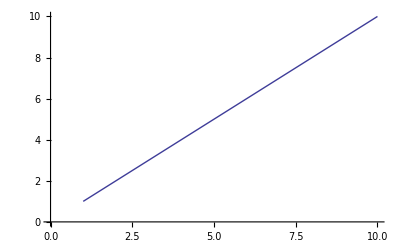

```mathematica
ListPlot[Range[10],Joined->True]
```

```mathematica
res ={}
```

{}

```mathematica
For[i=1,i<10,i++,(
res = Append[res,StageMinimize[i,initBatt][[1]]];
)]
```

NMinimize::argrx: NMinimize called with 3 arguments; 2 arguments are expected.

General::stop: Further output of NMinimize :: argrx will be suppressed during this calculation.

```mathematica
res
```

{524.626,603.697}

```mathematica
ListPlot[res,Joined->True]
```

```mathematica
$MachineEpsilon
```

2.22045×10^-16

```mathematica
e
```

```mathematica
Demand[t]
```

1331

```mathematica
firstStage
```

{49.3577 Null,{Null (xGB→0.),Null (xGC→0.),Null (xRB→0.),Null (xRC→2000.),Null (xRG→227.782),Null (xBC→0.),Null (xBG→100.),Null (yGB1→0.),Null (yGC1→0.),Null (yRB1→0.),Null (yRC1→2000.),Null (yRG1→161.615),Null (yBC1→0.),Null (yBG1→0.),Null (yGB2→0.),Null (yGC2→919.192),Null (yRB2→0.),Null (yRC2→1080.81),Null (yRG2→0.),Null (yBC2→0.),Null (yBG2→0.),Null (yGB3→0.),Null (yGC3→1459.6),Null (yRB3→0.),Null (yRC3→540.404),Null (yRG3→0.),Null (yBC3→0.),Null (yBG3→0.)}}

```mathematica
ClearAll["Global'*"]
```

```mathematica
firstStage
```

{28.5096 Null,{Null (xGB→0.),Null (xGC→0.),Null (xRB→0.),Null (xRC→2000.),Null (xRG→227.782),Null (xBC→0.),Null (xBG→100.),Null (yGB1→0.),Null (yGC1→0.),Null (yRB1→0.),Null (yRC1→2000.),Null (yRG1→161.615),Null (yBC1→0.),Null (yBG1→0.),Null (yGB2→0.),Null (yGC2→919.192),Null (yRB2→0.),Null (yRC2→1080.81),Null (yRG2→0.),Null (yBC2→0.),Null (yBG2→0.),Null (yGB3→0.),Null (yGC3→1459.6),Null (yRB3→1.13687×10^-13),Null (yRC3→540.404),Null (yRG3→0.),Null (yBC3→0.),Null (yBG3→0.)}}

```mathematica
$MachineEpsilon
```

2.22045×10^-16

```mathematica
wData[[All,20]]
```

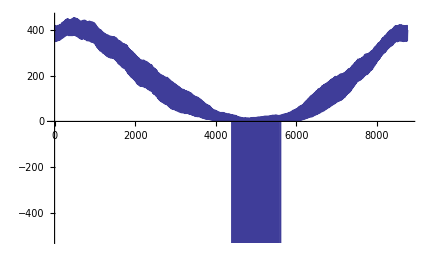

MaxValue::argbu: MaxValue called with 1 argument; between 2 and 4 arguments are expected.

454

```mathematica
ListPlot[wData[[All,3]],Joined->True]
```

```mathematica
Min[wData[[All,3]]]
```

-7777

```mathematica
wData[[All,10]]/10;
```

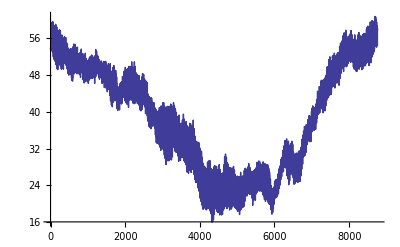

```mathematica
ListPlot[%,Joined->True]
```

```mathematica
%
```

{{xGB→0.,xGC→0.,xRB→0.,xRC→0.,xRG→2434.36,xBC→0.,xBG→10.,yGB1→0.,yGC1→0.,yRB1→0.,«8»,yRG2→1182.07,yBC2→0.,yBG2→0.,yGB3→0.,yGC3→0.,yRB3→0.,yRC3→0.,yRG3→591.035,yBC3→0.,yBG3→0.},«999»}

```mathematica
cloudOvercastPercentage[[4405]]
```

1/10

```mathematica
Demand[10]
```

7468

```mathematica
AvailableResource[10]
```

-1.18211×10^6

```mathematica
windSpeed[[10]]
```

4.87274

```mathematica
solarRadi[[Mod[t,24]+1,month]]
```

100

```mathematica
1-
```

```mathematica
0.5*windTurbineCoefficientFactor*windTurbineRadius^2*airDensity*Pi*windSpeed[[t]]^3+solarRadiationFactor*solarPanelSize*solarRadi[[Mod[t,24]+1,month]]*(1-cloudOvercastPercentage[[t]])
```

-404150.

```mathematica
(1-cloudOvercastPercentage[[t]])
```

-34

```mathematica
wData[[{10,1}]]
```

{{20100101 09:00,0,405,10087,10319,10203,175,127,98,551,50,-20,340,187,245,70,379,245,146,109,260,42,25,6,195,7,191},{20100101 00:00,0,405,10072,10299,10193,107,197,82,537,77,-9,340,188,245,81,390,245,151,103,262,43,32,7,223,6,209}}

```mathematica
wData[[t,1]]
```

20100101 14:00

```mathematica
wData[[1,1]]
```

20100101 00:00

```mathematica
ClearAll["Global`*"]
```

```mathematica
t=1000;
```

```mathematica
DateString[{wData[[t,1]],{"Year","Month","Day"," ","Hour",":","Minute"}},"Month"]//ToExpression
```

2

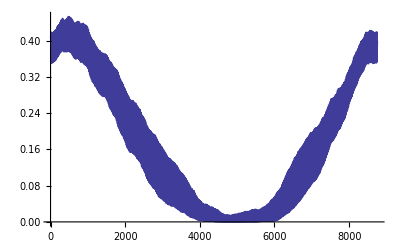

```mathematica
ListPlot[cloudOvercastPercentage[[All]],Joined->True]
```

```mathematica
firstStage
```

```mathematica
Dimensions[wData,1]
```

{8759}

```mathematica
[r1,r2]=StageMinimize[100,initBatt]
```

Syntax::sntxb: Expression cannot begin with "[r1, r2] = StageMinimize[100, initBatt]""".

Syntax::tsntxi: "[r1, r2]" is incomplete; more input is needed.""

Syntax::sntxi: Incomplete expression; more input is needed "".

```mathematica
$re = StageMinimize[100,initBatt]
```

{6019.1,{xGB→0.,xGC→40789.9,xRB→0.,xRC→2364.14,xRG→0.,xBC→10.,xBG→0.,yGB1→0.,yGC1→42670.7,yRB1→0.,yRC1→2295.29,yRG1→0.,yBC1→0.,yBG1→0.,yGB2→0.,yGC2→42720.4,yRB2→0.,yRC2→1147.64,yRG2→0.,yBC2→0.,yBG2→0.,yGB3→0.,yGC3→43452.2,yRB3→0.,yRC3→573.822,yRG3→0.,yBC3→0.,yBG3→0.}}

```mathematica
"t"/.$re
```

ReplaceAll::rmix: Elements of {6019.1, {xGB → 0., xGC → 40789.9, xRB → 0., xRC → 2364.14, xRG → 0., xBC → 10., xBG → 0., yGB1 → 0., yGC1 → 42670.7, yRB1 → 0., yRC1 → 2295.29, yRG1 → 0., yBC1 → 0., yBG1 → 0., yGB2 → 0., yGC2 → 42720.4, yRB2 → 0., yRC2 → 1147.64, yRG2 → 0., yBC2 → 0., yBG2 → 0., yGB3 → 0., yGC3 → 43452.2, yRB3 → 0., yRC3 → 573.822, yRG3 → 0., yBC3 → 0., yBG3 → 0.}} are a mixture of lists and nonlists.

t/.{6019.1,{xGB→0.,xGC→40789.9,xRB→0.,xRC→2364.14,xRG→0.,xBC→10.,xBG→0.,yGB1→0.,yGC1→42670.7,yRB1→0.,yRC1→2295.29,yRG1→0.,yBC1→0.,yBG1→0.,yGB2→0.,yGC2→42720.4,yRB2→0.,yRC2→1147.64,yRG2→0.,yBC2→0.,yBG2→0.,yGB3→0.,yGC3→43452.2,yRB3→0.,yRC3→573.822,yRG3→0.,yBC3→0.,yBG3→0.}}

```mathematica
new = {};

For[i=1,i<Dimensions[wData,1][[1]],i++,
(*Print[i];*)
firstStep = StageMinimize[i,initBatt];
new = Append[new,firstStep[[1]]];
initBatt = initBatt+(xRB/.firstStep[[2]])+(xGB/.firstStep[[2]])-(xBC/.firstStep[[2]])-(xBG/.firstStep[[2]]);
secondStep = StageMinimize[i+1,initBatt];
]
```

Part::pspec: Part specification $Failed is neither a machine-sized integer nor a list of machine-sized integers.

ToExpression::notstrbox: DateString[{{{"20100101 00:00", 0, 405, 10072, 10299, 10193, 107, 197, 82, 537, 77, -9, 340, 188, 245, 81, 390, 245, 151, 103, 262, 43, 32, 7, 223, 6, 209}, {"20100101 01:00", 0, 408, 10076, 10301, 10191, 125, 209, 77, 540, 50, -20, 340, 186, 242, 70, 379, 242, 148, 102, 262, 43, 47, 7, 218, 6, 215}, {"20100101 02:00", 0, 411, 10075, 10303, 10193, 142, 223, 43, 534, 59, -20, 340, 186, 239, 70, 379, 239, 146, 100, 261, 40, 45, 6, 234, 7, 201}, « 46 », {"20100103 01:00", 0, 406, 10068, 10304, 10190, 134, 210, 71, 531, 55, -9, 340, 189, 244, 70, 392, 244, 150, 103, 262, 42, 38, 7, 207, 6, 196}, « 8709 »} ⟦ 8760, 1 ⟧, {"Year", « 5 », "Minute"}}, "Month"] is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

Part::pspec: Part specification $Failed is neither a machine-sized integer nor a list of machine-sized integers.

DateString::arg: Argument {{{"20100101 00:00", 0, 405, 10072, 10299, 10193, 107, 197, 82, 537, 77, -9, 340, 188, 245, 81, 390, 245, 151, 103, 262, 43, 32, 7, 223, 6, 209}, {"20100101 01:00", 0, 408, 10076, 10301, 10191, 125, 209, 77, 540, 50, -20, 340, 186, 242, 70, 379, 242, 148, 102, 262, 43, 47, 7, 218, 6, 215}, {"20100101 02:00", 0, 411, 10075, 10303, 10193, 142, 223, 43, 534, 59, -20, 340, 186, 239, 70, 379, 239, 146, 100, 261, 40, 45, 6, 234, 7, 201}, « 46 », {"20100103 01:00", 0, 406, 10068, 10304, 10190, 134, 210, 71, 531, 55, -9, 340, 189, 244, 70, 392, 244, 150, 103, 262, 42, 38, 7, 207, 6, 196}, « 8709 »} ⟦ 8760, 1 ⟧, {"Year", "Month", "Day", " ", "Hour", ":", "Minute"}} cannot be interpreted as a date or time input or as a date string format.

General::stop: Further output of DateString :: arg will be suppressed during this calculation.

ToExpression::notstrbox: DateString[{{{"20100101 00:00", 0, 405, 10072, 10299, 10193, 107, 197, 82, 537, 77, -9, 340, 188, 245, 81, 390, 245, 151, 103, 262, 43, 32, 7, 223, 6, 209}, {"20100101 01:00", 0, 408, 10076, 10301, 10191, 125, 209, 77, 540, 50, -20, 340, 186, 242, 70, 379, 242, 148, 102, 262, 43, 47, 7, 218, 6, 215}, {"20100101 02:00", 0, 411, 10075, 10303, 10193, 142, 223, 43, 534, 59, -20, 340, 186, 239, 70, 379, 239, 146, 100, 261, 40, 45, 6, 234, 7, 201}, « 46 », {"20100103 01:00", 0, 406, 10068, 10304, 10190, 134, 210, 71, 531, 55, -9, 340, 189, 244, 70, 392, 244, 150, 103, 262, 42, 38, 7, 207, 6, 196}, « 8709 »} ⟦ 8760, 1 ⟧, {"Year", « 5 », "Minute"}}, "Month"] is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

Part::pspec: Part specification $Failed is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

```mathematica
new
```

{4779.45,5952.47,5042.92,6038.81,5052.38,10094.3,11190.4,9993.33,5427.73,6009.8,4984.57,3810.85,5252.62,4053.14,«8731»,5207.79,2893.51,3653.11,5598.32,6064.05,5199.48,8469.99,8116.51,10449.4,11121.7,9303.26,6463.96,5836.32}

```mathematica
firstStep
```

{6045.5,{xGB→0.,xGC→43161.9,xRB→0.,xRC→2364.14,xRG→0.,xBC→0.,xBG→0.,yGB1→0.,yGC1→39511.9,yRB1→0.,yRC1→2364.14,yRG1→0.,yBC1→0.,yBG1→0.,yGB2→0.,yGC2→43075.9,yRB2→0.,yRC2→1182.07,yRG2→0.,yBC2→0.,yBG2→0.,yGB3→0.,yGC3→43747.,yRB3→0.,yRC3→591.035,yRG3→0.,yBC3→0.,yBG3→0.}}

```mathematica
firstStep = StageMinimize[i,initBatt];
```

```mathematica
firstStep[[1]]
```

4821.13

```mathematica
Append[new,firstStep[[1]]]
```

{6045.5}

```mathematica
new
```

{}

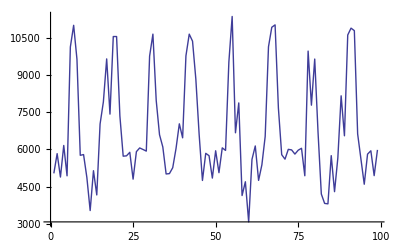

```mathematica
ListPlot[new,Joined->True]
```

```mathematica
Dimensions[wData,1][[1]]
```

8759

```mathematica
Length[new]
```

8758

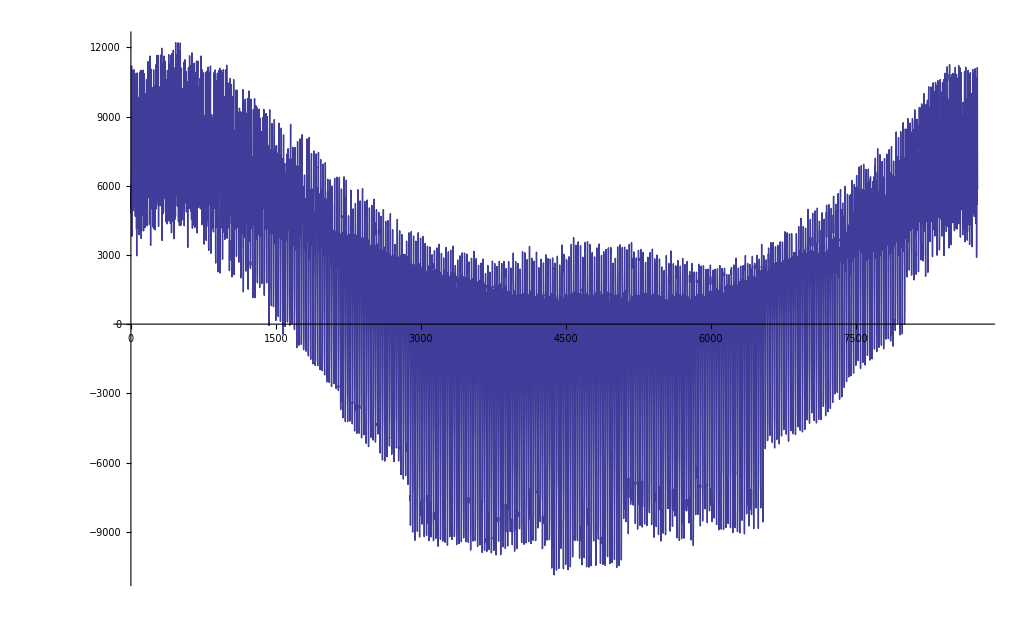

```mathematica
ListPlot[new[[All]],Joined->True]
```

```mathematica
Min[new]
```

-10874.7

```mathematica
cost = {};
bat = {initBatt};
For[t=1,t<Dimensions[wData,1][[1]]-1,t++,
firstStep = StageMinimize[t,initBatt];
cost = Append[cost,firstStep[[1]]];
initBatt = initBatt+(xRB/.firstStep[[2]])+(xGB/.firstStep[[2]])-(xBC/.firstStep[[2]])-(xBG/.firstStep[[2]]);
bat = Append[bat,initBatt];
secondStep = StageMinimize[t+1,initBatt];
]
```

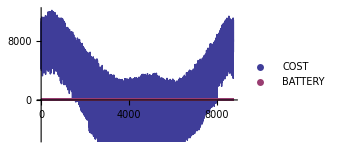

```mathematica
ListPlot[{cost, bat},Joined->True,PlotLegends->{"COST","BATTERY"}]
```

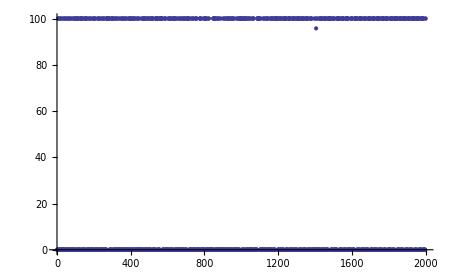

```mathematica
ListPlot[bat[[1;;2000]],PlotLegends->"BATTERY"]
```

```mathematica
DayOfWeek
```

DayOfWeek

```mathematica
Needs["Calendar`"]
```

DayOfWeek::shdw: Symbol "DayOfWeek" appears in multiple contexts {"Calendar`", "Global`"}; definitions in context "Calendar`" may shadow or be shadowed by other definitions.

```mathematica
<<Calendar`
```

```mathematica
DayOfWeek[{2010,1,1}]
```

Friday

```mathematica
wData[[100,1]]
```

20100105 03:00

```mathematica
DateString[{wData[[100,1]],{"Year","Month","Day"," ","Hour",":","Minute"}},"Year"]//ToExpression
```

2010

```mathematica
MemberQ[{Saturday,Sunday},DayOfWeek[{2014,3,30}]]
```

True

```mathematica
BuyPrice[400]
```

0.051

```mathematica
For[i=1,i<1000,i++,Print[dayOfWeek[i]]]
```

```mathematica
MemberQ[{Saturday,Sunday},dayOfWeek[50]]
```

True

```mathematica
Table[dayOfWeek[i],{i,1,Dimensions[wData,1][[1]]}]//Timing
```

```mathematica
ClearAll["Global`*"]
```

## Three-stage SP Test:

```mathematica
<<Calendar`
(* Definition of functions to work on simulation part. *)
wData = Import["wt_data.csv","CSV",Path->NotebookDirectory[],"HeaderLines"->1];
solarRadi = Import["solar.txt","Table",Path-> NotebookDirectory[]];
markovChainMatrix = {{0.7,0.2,0.1},{0.6,0.3,0.1},{0.5,0.4,0.1}};
stateProb = markovChainMatrix[[1]].MatrixPower[markovChainMatrix,10];
randomStateSequence = RandomChoice[stateProb->{"N","A","M"},Dimensions[wData][[1]]];

(* Extract wind and time data *)
windSpeed = wData[[All,20]]/10*0.44704;
coolingDegreeHours = (wData[[All,2]]/.-7777->0)/10;
heatDegreeHours = (wData[[All,3]]/.-7777->0)/10;
cloudOvercastPercentage = ((wData[[All,3]])/.-7777->0)/10/100;
year[t_]:=(
DateString[{wData[[t,1]],{"Year","Month","Day"," ","Hour",":","Minute"}},"Year"]//ToExpression
);
month[t_]:=(
DateString[{wData[[t,1]],{"Year","Month","Day"," ","Hour",":","Minute"}},"Month"]//ToExpression
);
day[t_]:=(
DateString[{wData[[t,1]],{"Year","Month","Day"," ","Hour",":","Minute"}},"Day"]//ToExpression
);
dayOfWeek[t_]:=(
DayOfWeek[{year[t],month[t],day[t]}]
);
(* Define Price of buying and selling. *)
BuyPrice[t_]:= (
If[MemberQ[{Saturday,Sunday},dayOfWeek[t]],0.051,
If[7≤ Mod[t,24]<11||17<Mod[t,24]≤ 21,0.099,
If[11≤Mod[t,24]≤ 17,0.081,
0.051
]
]
]
);
SellPrice[t_]:= 0.8*BuyPrice[t];

(* Initialize stages, currently two stages. *)
stageSize = 2;
availableResources = Table[0, {i,stageSize}];
demand = Table[0,{i, stageSize}];

(* Initial values to parameters. *)
airDensity = 1.27;
windTurbineCoefficientFactor = 0.5;
windTurbineRadius = 5;
solarRadiationFactor = 1.2;
solarPanelSize = 100;
initBatt =100;
t=15;
capBat=1000;

(* Function of Available Resources at time t: electricity power from wind energy and solar energy *)
AvailableResource[t_]:=(
0.5*windTurbineCoefficientFactor*windTurbineRadius^2*airDensity*Pi*windSpeed[[t]]^3+solarRadiationFactor*solarPanelSize*solarRadi[[Mod[t,24]+1,month[t]]]*(1-cloudOvercastPercentage[[t]])
);
(* Function of Local Demand at time t: pick a random integer from 1000 to 10000 *)
Demand[t_]:=(
(*If[t==18,100000,AvailableResource[t]+1000]*)
pLossRate = 1000;
heatDegreeHours[[t]]*pLossRate+coolingDegreeHours[[t]]*pLossRate+RandomInteger[{500,5000}]
(*RandomInteger[{1000,10000}]*)
);
(* Function of unit cost of reserving electricity in battery : set it constant *)
ReserveCost[t_]:=(0.02);
(* Function of unit cost of transiting electricity to or from battery : set it constant *)
TransitionCost[t_]:=(0.01);

(* Function of optimization of simple two-stage *)
(* 
	B->C:1,
	B->G:2,
	G->B:3,
	G->C:4,
	R->B:5,
	R->C:6,
	R->G:7
*)

StageMinimize[t_,initBatt_]:=(
Minimize[
{
(x[3]+x[4])*BuyPrice[t]+
(initBatt+x[3]+x[5]-x[1]-x[2])*ReserveCost[t] + 
(initBatt+x[3]+x[5]+x[1]+x[2])*TransitionCost[t]-
(x[2]+x[7])*SellPrice[t]+

If[randomStateSequence[[t]]=="N",markovChainMatrix[[1,1]],
If[randomStateSequence[[t]]=="A",markovChainMatrix[[2,1]],
markovChainMatrix[[3,1]]]]*(
	(y[3,1]+y[4,1])*BuyPrice[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]-y[1,1]-y[2,1])*ReserveCost[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,1]+y[5,1]+y[1,1]+y[2,1])*TransitionCost[t+1]-
	(y[2,1]+y[7,1])*SellPrice[t+1])+

If[randomStateSequence[[t]]=="N",markovChainMatrix[[1,2]],
If[randomStateSequence[[t]]=="A",markovChainMatrix[[2,2]],
markovChainMatrix[3,2]]]*(
	(y[3,2]+y[4,2])*BuyPrice[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]-y[1,2]-y[2,2])*ReserveCost[t+1]+  
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,2]+y[5,2]+y[1,2]+y[2,2])*TransitionCost[t+1]-
		(y[2,2]+y[7,2])*SellPrice[t+1])+

If[randomStateSequence[[t]]=="N",markovChainMatrix[[1,3]],
If[randomStateSequence[[t]]=="A",markovChainMatrix[[2,3]],
markovChainMatrix[[3,3]]]]*(
	(y[3,3]+y[4,3])*BuyPrice[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]-y[1,3]-y[2,3])*ReserveCost[t+1]+
	((initBatt+x[3]+x[5]-x[1]-x[2])+y[3,3]+y[5,3]+y[1,3]+y[2,3])*TransitionCost[t+1]-
	(y[2,3]+y[7,3])*SellPrice[t+1]),

x[1]+x[4]+x[6]==Demand[t]&&
0≤ initBatt+x[5]+x[3]-x[2]-x[1]≤ capBat&&
x[7]+x[5]+x[6]==AvailableResource[t]&&
x[3]≥0&&x[4]≥0&&x[5]≥0&&x[6]≥0&&x[7]≥0&&x[1]≥0&&x[2]≥0&&


y[1,1]+y[4,1]+y[6,1]==Demand[t+1]&&
-(initBatt+x[3]+x[5]-x[1]-x[2])≤ y[5,1]+y[3,1]-y[2,1]-y[1,1]≤ capBat-(initBatt+x[3]+x[5]-x[1]-x[2])&&
y[7,1]+y[5,1]+y[6,1]==AvailableResource[t+1]&&
y[3,1]≥0&&y[4,1]≥0&&y[5,1]≥0&&y[6,1]≥0&&y[7,1]≥0&&y[1,1]≥0&&y[2,1]≥0&&

y[1,2]+y[4,2]+y[6,2]==Demand[t+1]&&
-(initBatt+x[3]+x[5]-x[1]-x[2])≤ y[5,2]+y[3,2]-y[2,2]-y[1,2]≤ capBat-(initBatt+x[3]+x[5]-x[1]-x[2])&&
y[7,2]+y[5,2]+y[6,2]==AvailableResource[t+1]/2&&
y[3,2]≥0&&y[4,2]≥0&&y[5,2]≥0&&y[6,2]≥0&&y[7,2]≥0&&y[1,2]≥0&&y[2,2]≥0&&

y[1,3]+y[4,3]+y[6,3]==Demand[t+1]&&
-(initBatt+x[3]+x[5]-x[1]-x[2])≤ y[5,3]+y[3,3]-y[2,3]-y[1,3]≤ capBat-(initBatt+x[3]+x[5]-x[1]-x[2])&&
y[7,3]+y[5,3]+y[6,3]==AvailableResource[t+1]/4&&
y[3,3]≥0&&y[4,3]≥0&&y[5,3]≥0&&y[6,3]≥0&&y[7,3]≥0&&y[1,3]≥0&&y[2,3]≥0
},
{x[3],x[4],x[5],x[6],x[7],x[1],x[2],y[3,1],y[4,1],y[5,1],y[6,1],y[7,1],y[1,1],y[2,1],y[3,2],y[4,2],y[5,2],y[6,2],y[7,2],y[1,2],y[2,2],y[3,3],y[4,3],y[5,3],y[6,3],y[7,3],y[1,3],y[2,3]}]
);
```

```mathematica
1.2*10^-12
```

1.2×10^-12

```mathematica
N[%,2]
```

1.2×10^-12

```mathematica
%`2
```

```mathematica
1.2*^-12`2
```